```mathematica
psi1[x_] := AA Sin[k * x]
```

```mathematica
psi2[x_] := Exp[-I k x] + SS Exp[I k x]
```

```mathematica
Solve[{
psi1[aa] == psi2[aa],
psi2'[aa] - psi1'[aa] == uu psi1[aa]}, {AA, SS}]
```

{{AA→(2 ⅇ^(-ⅈ aa k) k)/(ⅈ k Cos[aa k]+k Sin[aa k]+ⅈ uu Sin[aa k]),SS→-ⅇ^(-2 ⅈ aa k)+(2 ⅇ^(-2 ⅈ aa k) k Sin[aa k])/(ⅈ k Cos[aa k]+k Sin[aa k]+ⅈ uu Sin[aa k])}}

```mathematica
SS := -ⅇ^(-2 ⅈ aa k)+(2 ⅇ^(-2 ⅈ aa k) k Sin[aa k])/(ⅈ k Cos[aa k]+k Sin[aa k]+ⅈ uu Sin[aa k])
```

```mathematica
shift[k_] := Arg[SS]
```

```mathematica
aa := 1
```

```mathematica
uu := 1
```

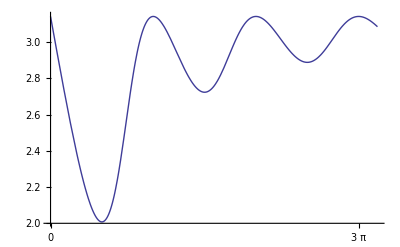

```mathematica
Plot[shift[k], {k, 0.0, 10.0}, Ticks->{Range[0, 10 * Pi, Pi], Automatic}]
```